```mathematica
i="1"
```

1

```mathematica
fileApproxLU="/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxLU"<>i<>".txt";
fileApproxLC="/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxLC"<>i<>".txt";

fileApproxCUB="/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxCUB1.txt";

fileAccurLU="/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxLU1.txt";
fileAccurLC="/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxLC1.txt";
fileAccurCUB="/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxCUB1.txt";
```

/home/andrey/CLionProjects/NumericalMethods/Lab3/files/approxLU1.txt

```mathematica
dataApproxLU = Import[fileApproxLU,"CSV"];
dataApproxLC = Import[fileApproxLC,"CSV"];
dataApproxCUB = Import[fileApproxCUB,"CSV"];
dataAccurLU = Import[fileAccurLU,"CSV"];
dataAccurLC = Import[fileAccurLC,"CSV"];
dataAccurCUB = Import[fileAccurCUB,"CSV"];
```

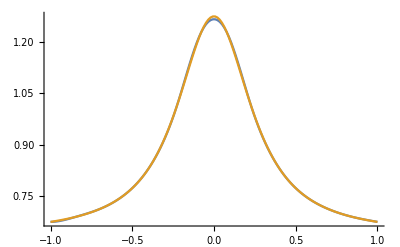

```mathematica
ListLinePlot[{dataApprox,dataAccur}]
```

```mathematica
|
```